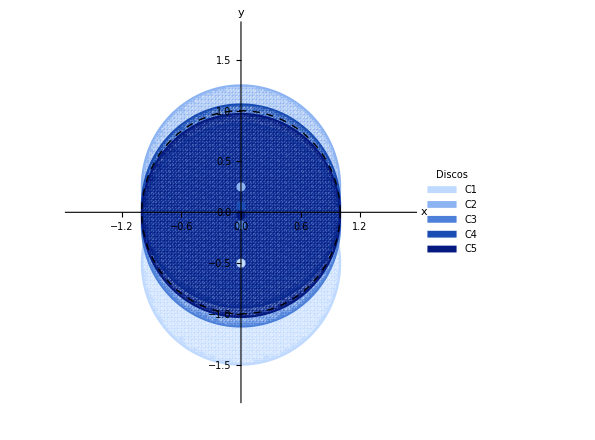

```mathematica
nMax=5;
yCenters=Table[(-1/2)^n,{n,1,nMax}];
colores={RGBColor[0.75,0.85,1],RGBColor[0.55,0.7,0.95],RGBColor[0.3,0.5,0.85],RGBColor[0.1,0.3,0.7],RGBColor[0.02,0.1,0.5]};
etiquetas=Table["C"<>ToString[n],{n,1,nMax}];

grafico=Show[Table[RegionPlot[x^2+(y-yCenters[[n]])^2<=1,{x,-1.7,1.7},{y,-1.8,1.8},PlotStyle->Directive[colores[[n]],Opacity[0.4]],BoundaryStyle->Directive[colores[[n]],Thickness[0.003]],PlotPoints->100],{n,1,nMax}],Graphics[{{Dashed,Thick,Black,Circle[{0,0},1]},Table[{colores[[n]],PointSize[0.015],Point[{0,yCenters[[n]]}]},{n,1,nMax}]}],Axes->True,AxesOrigin->{0,0},AxesLabel->{Style["x",18],Style["y",18]},TicksStyle->Directive[FontSize->14],Frame->False,AspectRatio->1,ImageSize->440,PlotRange->{{-1.7,1.7},{-1.8,1.8}}];

Legended[grafico,SwatchLegend[colores,etiquetas,LegendLabel->Style["Discos",16],LabelStyle->Directive[FontSize->16],LegendMarkerSize->18]]
```

```mathematica
Export["C:\\Users\\jesus\\Desktop\\Universidad\\Teoría de la probabilidad\\Latex_Teoria_Probabilidad\\imagenes\\problemas_Quesada\\prob_quesada_1_19_a.png",%39,"PNG"]
```

C:\Users\jesus\Desktop\Universidad\Teoría de la probabilidad\Latex_Teoria_Probabilidad\imagenes\problemas_Quesada\prob_quesada_1_19_a.png